I remind that last week I completed a circuit by inputting concentrations and outputting concentrations.

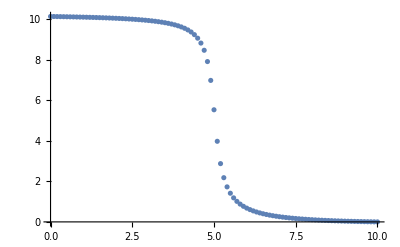

```mathematica
Clear[enhancedGRN5];
enhancedGRN5[Rconc_,Cconc_,k1_:1.0,ktx_:500.0,kON_:100.0,kOFF_:25,tot_:10,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0,kftx_:5.2]:=
Module[{null,r,c,rG1,cG1c,G1,G1c,T1,T1c,R1,C1,sol,rsys,OFF,ON,T,OUT},
rsys={
(* Gene R1 *)
revrxn[r+G1,rG1,k1,k1],
rxn[rG1,rG1+T1,ktx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Titrant Gene C1 *)
revrxn[c+G1c,cG1c,k1,k1],
rxn[cG1c,cG1c+T1c,ktx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

(* Titration *)
rxn[C1+R1,null,kc],

(* "Reporter" Gene *)
revrxn[R1+OFF,ON,kON,kOFF],
rxn[ON,ON+T,kftx],
rxn[T,T+OUT,ktl],
rxn[T,null,krd],
rxn[OUT,null,kpd],

conc[r,Rconc],
conc[c,Cconc],
conc[G1,1],
conc[G1c,1],
conc[OFF,tot]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{OUT[t]}/.sol]
]
plotter=enhancedGRN5[2,5];
enhancedGRN5Plot[r_,c_]:=(
plotter=enhancedGRN5[r,c];
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"G1f" ])

tmax=60;
c=5;

Manipulate[enhancedGRN5Plot[a,5],{a,0,10}]
y=Table[{10-i,enhancedGRN5[i,c][[1]][[0]][tmax]},{i,0,10,0.1}];
ListPlot[y]
```

First, I would like to reduce the concentration of titrant as an input parameter. So exactly 1 input for a GRN corresponds to exactly 1 output.

(Actually, I don’t really need this, but I guess it’s a proof-of-concept that it can still work. In my work below, I just go back to the old way, as I find it simpler to abstract away a GRN).

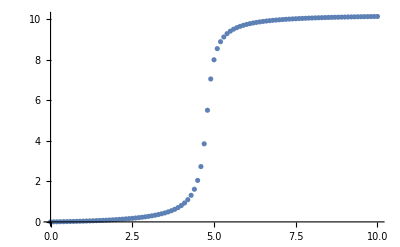

```mathematica
Clear[enhancedGRN6];
enhancedGRN6[Rconc_,k1_:1.0,ktx_:500.0,kON_:100.0,kOFF_:25,tot_:10,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0,kftx_:5.2]:=
Module[{null,r,rG1,cG1c,G1,G1c,T1,T1c,R1,C1,sol,rsys,OFF,ON,T,OUT},
kctx=400.0;
rsys={
(* Gene R1 *)
revrxn[r+G1,rG1,k1,k1],
rxn[rG1,rG1+T1,ktx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Titrant Gene C1 *)
rxn[G1c,G1c+T1c,kctx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

(* Titration *)
rxn[C1+R1,null,kc],

(* "Reporter" Gene *)
revrxn[R1+OFF,ON,kON,kOFF],
rxn[ON,ON+T,kftx],
rxn[T,T+OUT,ktl],
rxn[T,null,krd],
rxn[OUT,null,kpd],

conc[r,Rconc],
conc[G1,1],
conc[G1c,1],
conc[OFF,tot]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{OUT[t]}/.sol]
]
enhancedGRN6Plot[r_]:=(
plotter=enhancedGRN6[r];
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"G1f" ])

tmax=60;
c=5;

Manipulate[enhancedGRN6Plot[a],{a,0,10}]
y=Table[{i,enhancedGRN6[i][[1]][[0]][tmax]},{i,0,10,0.1}];
ListPlot[y]
```

Titrant Module

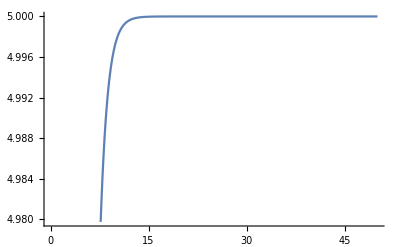

```mathematica
titrantGRN[gene_]:=Module[{null},
(* Gene C1 *)
gn=Symbol["G"<>gene<>"C"];
ts=Symbol["T"<>gene<>"C"];
out=Symbol["C"<>gene];
Seq[
rxn[gn,gn+ts,ktx],
rxn[ts,ts+out,ktl],
rxn[ts,null,krd],
rxn[out,null,kpd],
conc[gn,c]
]
]

ktx=5.0;
ktl=krd=kpd=1.0;
c=1;
tmax=50;
rsys={
titrantGRN["X"]
};
sol=SimulateRxnsys[rsys,tmax];
plotter={Symbol["C"<>"X"][t]}/.sol;
Plot[plotter,{t,0,50}]
```

This works as desired (see the sample circuit I built last week). Now I will build parts of the other genes, and continue abstracting away parts of the enhanced GRN model.

```mathematica
Clear[GRN]
GRN[{IN_,OUT_},init_:{x[0]==0},kON_:1.0,kOFF_:1.0]:=Module[{null,initIN},
(* Gene A1 *)
With[
{c=
Cases[init,v_[0]== b_ ->b]},
initIN=c[[1]]];

out=ToString[OUT];
in=ToString[IN];
gn=Symbol["GN"<>out];
ts=Symbol["TS"<>out];
actGene=Symbol[in<>ToString[gn]];
Seq[
revrxn[IN+gn,actGene,kON,kOFF],
rxn[actGene,actGene+ts,ktx],
rxn[ts,ts+OUT,ktl],
rxn[ts,null,krd],
rxn[OUT,null,kpd],

conc[IN,initIN],
conc[gn,Gtot]

]
]
```

{X+GNY →^1. XGNY ,XGNY →^1. X+GNY ,XGNY →^5. XGNY+TSY ,TSY →^1. TSY+Y ,TSY →^5. null$269822 ,Y →^1. null$269822 ,conc[X,1],conc[GNY,10],Y+GNZ →^1. YGNZ ,YGNZ →^1. Y+GNZ ,YGNZ →^5. YGNZ+TSZ ,TSZ →^1. TSZ+Z ,TSZ →^5. null$269823 ,Z →^1. null$269823 ,conc[Y,0],conc[GNZ,10]}

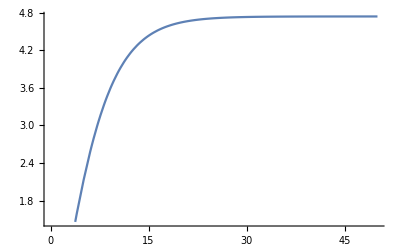

```mathematica
Clear[Gtot,ktl,krd,kpd,ktx,X,Y,Z]
tmax=50;
Gtot=10;
ktl=kpd=1.0;
krd=5.0;
ktx=5.0;
dummySys={
GRN[{X,Y},{X[0]==1}],
GRN[{Y,Z}]
}

sol=SimulateRxnsys[dummySys,tmax];
plotter={Z[t]}/.sol;
Plot[plotter,{t,0,50}]
```

{X+GNAY →^1. XGNAY ,XGNAY →^1. X+GNAY ,XGNAY →^60. XGNAY+TSAY ,TSAY →^1. TSAY+AY ,TSAY →^5. null$4381 ,AY →^1. null$4381 ,conc[X,10],conc[GNAY,1],t$4380+GNTY →^1. t$4380GNTY ,t$4380GNTY →^1. t$4380+GNTY ,t$4380GNTY →^60. t$4380GNTY+TSTY ,TSTY →^1. TSTY+TY ,TSTY →^5. null$4382 ,TY →^1. null$4382 ,conc[t$4380,5],conc[GNTY,1],TY+AY →^1000 null$4380 ,AY+GNY →^110 AYGNY ,AYGNY →^25 AY+GNY ,AYGNY →^60. AYGNY+TSY ,TSY →^1. TSY+Y ,TSY →^5. null$4383 ,Y →^1. null$4383 ,conc[AY,0],conc[GNY,1]}

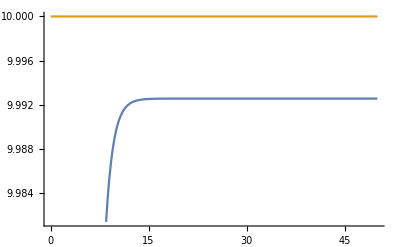

```mathematica
Clear[GRN]
GRN[{IN_,OUT_},init_:{x[0]==0},kON_:1.0,kOFF_:1.0]:=Module[{null,initIN,kpd,ktx,ktl,krd,Gtot},
(* Gene A1 *)
With[
{c=
Cases[init,v_[0]== b_ ->b]},
initIN=c[[1]]];
ktx=60.0;
ktl=kpd=1.0;
krd=5.0;
Gtot=1;
out=ToString[OUT];
in=ToString[IN];
gn=Symbol["GN"<>out];
ts=Symbol["TS"<>out];
actGene=Symbol[in<>ToString[gn]];
Seq[
revrxn[IN+gn,actGene,kON,kOFF],
rxn[actGene,actGene+ts,ktx],
rxn[ts,ts+OUT,ktl],
rxn[ts,null,krd],
rxn[OUT,null,kpd],

conc[IN,initIN],
conc[gn,Gtot]

]
]

Clear[titrationGRN]
titrationGRN[{IN_,OUT_},init_:{x[0]==0}]:=Module[{null,initT,rptrON,rptrOFF,kc,t,in,out,titr,anyl},
in=ToString[IN];
out=ToString[OUT];
titr=Symbol["T"<>out];
anyl=Symbol["A"<>out];
rptrON=110;
rptrOFF=25;
kc=1000;
Seq[
(* analyte *)
GRN[{IN,anyl},init],

(* titrant *)
GRN[{t,titr},{t[0]==5}],

(* titrant rxn *)
rxn[titr+anyl,null,kc],

(* reporter *)
GRN[{anyl,OUT},{anyl[0]==0},rptrON,rptrOFF]
]
]
Clear[X,Y];
tmax=50;
dummySys2={
titrationGRN[{X,Y},{X[0]==10}]
}
sol=SimulateRxnsys[dummySys2,tmax];
plotter={Y[t]}/.sol;
Plot[{plotter,10},{t,0,50}]
```

```mathematica
Clear[A,B]

GRNSim[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];

sol=SimulateRxnsys[rsys,time];
plotter=(#[t]&/@watch)/.sol
)


GRNSimPlot[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];
sol=SimulateRxnsys[rsys,time];
plotter=(#[t]&/@watch)/.sol;
Plot[plotter,{t,0,time},PlotRange->All,
PlotLegends->watch]
)

tmax=20;
Manipulate[GRNSimPlot[{titrationGRN[{A,B},{A[0]==i}]},{B},20],{i,0,10}]
```

NDSolve::deqn: Equation or list of equations expected instead of titrationGRN[{A, B}, {A[0] == 10.}] in the first argument {titrationGRN[{A, B}, {A[0] == 10.}]}.

ReplaceAll::reps: {titrationGRN[{A, B}, {A[0] == 10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {titrationGRN[{A, B}, {A[0.] == 10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

9.45696

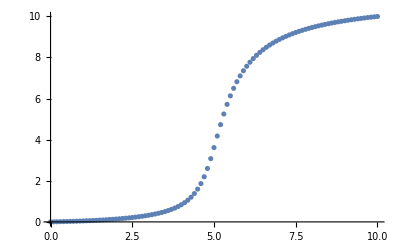

```mathematica
GRNSim[{titrationGRN[{A,B},{A[0]==8}]},{B},tmax][[1]][[0]][tmax]
tmax=20;
y=Table[{i,GRNSim[{titrationGRN[{A,B},{A[0]==i}]},{B},tmax][[1]][[0]][tmax]},{i,0,10,0.1}];
ListPlot[y]
```

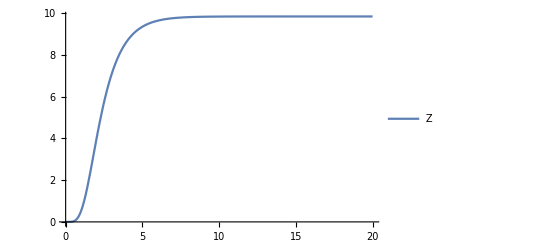

```mathematica
GRNSimPlot[{GRN[{X,Y},{X[0]==1}],GRN[{Y,Z}]},{Z},tmax]
```

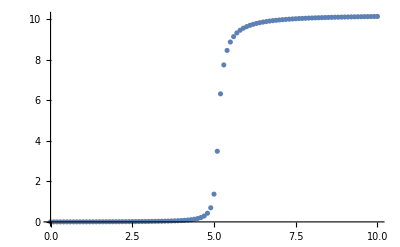

```mathematica
titrCurves[low_,high_,step_]:=(
y=Table[{i,GRNSim[{titrationGRN[{X,Y},{X[0]==i}],titrationGRN[{Y,Z},{Y[0]==0}]},{Z},tmax][[1]][[0]][tmax]},{i,low,high,step}];
ListPlot[y]
)

titrCurves[0,10,0.1]
```

Working on thresholding before adding now

A

B

Scratch Paper

```mathematica
Clear[initX];
With[
{init=
Cases[{x[0]==3.4},v_[0]== b_ ->b]},
initX=init];
initX
Flatten[
{
titrationGRN[{X,Y},{X[0]==10}],
titrationGRN[{Y,Z},{Y[0]==0}]
}]
```

{3.4}

{X+GNAY →^1. XGNAY ,XGNAY →^1. X+GNAY ,XGNAY →^60. XGNAY+TSAY ,TSAY →^1. TSAY+AY ,TSAY →^5. null$333406 ,AY →^1. null$333406 ,conc[X,10],conc[GNAY,1],t$333405+GNTY →^1. t$333405GNTY ,t$333405GNTY →^1. t$333405+GNTY ,t$333405GNTY →^60. t$333405GNTY+TSTY ,TSTY →^1. TSTY+TY ,TSTY →^5. null$333407 ,TY →^1. null$333407 ,conc[t$333405,5],conc[GNTY,1],TY+AY →^1000 null$333405 ,AY+GNY →^110 AYGNY ,AYGNY →^25 AY+GNY ,AYGNY →^60. AYGNY+TSY ,TSY →^1. TSY+Y ,TSY →^5. null$333408 ,Y →^1. null$333408 ,conc[AY,0],conc[GNY,1],Y+GNAZ →^1. YGNAZ ,YGNAZ →^1. Y+GNAZ ,YGNAZ →^60. YGNAZ+TSAZ ,TSAZ →^1. TSAZ+AZ ,TSAZ →^5. null$333410 ,AZ →^1. null$333410 ,conc[Y,0],conc[GNAZ,1],t$333409+GNTZ →^1. t$333409GNTZ ,t$333409GNTZ →^1. t$333409+GNTZ ,t$333409GNTZ →^60. t$333409GNTZ+TSTZ ,TSTZ →^1. TSTZ+TZ ,TSTZ →^5. null$333411 ,TZ →^1. null$333411 ,conc[t$333409,5],conc[GNTZ,1],TZ+AZ →^1000 null$333409 ,AZ+GNZ →^110 AZGNZ ,AZGNZ →^25 AZ+GNZ ,AZGNZ →^60. AZGNZ+TSZ ,TSZ →^1. TSZ+Z ,TSZ →^5. null$333412 ,Z →^1. null$333412 ,conc[AZ,0],conc[GNZ,1]}

```mathematica
?Complement
?With
?Cases
?#
?&
?Sequence
```

RowBox[{"Complement", "[", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["all", "TI"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] gives the elements in SubscriptBox[StyleBox["e", "TI"], StyleBox["all", "TI"]] that are not in any of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]].

RowBox[{"With", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], ",", RowBox[{StyleBox["y", "TI"], "=", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["expr", "TI"]}], "]"}] specifies that all occurrences of the symbols StyleBox["x", "TI"], StyleBox["y", "TI"], … in StyleBox["expr", "TI"] should be replaced by SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]], ….

RowBox[{"Cases", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["pattern", "TI"]}], "]"}] gives a list of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] that match the pattern. 
RowBox[{"Cases", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{StyleBox["pattern", "TI"], "→", StyleBox["rhs", "TI"]}]}], "]"}] gives a list of the values of StyleBox["rhs", "TI"] corresponding to the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] that match the pattern. 
RowBox[{"Cases", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] gives a list of all parts of StyleBox["expr", "TI"] on levels specified by StyleBox["levelspec", "TI"] that match the pattern. 
RowBox[{"Cases", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{StyleBox["pattern", "TI"], "→", StyleBox["rhs", "TI"]}], ",", StyleBox["levelspec", "TI"]}], "]"}] gives the values of StyleBox["rhs", "TI"] that match the pattern. 
RowBox[{"Cases", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the first StyleBox["n", "TI"] parts in StyleBox["expr", "TI"] that match the pattern. 
RowBox[{"Cases", "[", StyleBox["pattern", "TI"], "]"}] represents an operator form of Cases that can be applied to an expression.

# represents the first argument supplied to a pure function. 
StyleBox[RowBox[{"#", StyleBox["n", "TI"]}]] represents the StyleBox[RowBox[{StyleBox["n", "TI"], ""}]]SuperscriptBox["", "th"] argument. 
StyleBox[RowBox[{"#", StyleBox["name", "TI"]}]] represents the value associated with key "
StyleBox["name", "TI"]" in an association in the first argument.

RowBox[{"Function", "[", StyleBox["body", "TI"], "]"}] or RowBox[{StyleBox["body", "TI"], "&"}] is a pure function. The formal parameters are # (or #1), #2, etc. 
RowBox[{"Function", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["body", "TI"]}], "]"}] is a pure function with a single formal parameter StyleBox["x", "TI"]. 
RowBox[{"Function", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["body", "TI"]}], "]"}] is a pure function with a list of formal parameters.

RowBox[{"Sequence", "[", RowBox[{SubscriptBox[StyleBox["expr", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["expr", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] represents a sequence of arguments to be spliced automatically into any function.